# Amitosis

We try to predict the change in the mean number of mutations at a single locus (k̄) in a population as a result of selection, mutation and reproduction by mitosis.  We model the distribution directly.

## Model

### Parameters

f_k, frequency of genotype with k mutations
w̄, mean fitness
ŵ, mean fitness at equilibrium
k̄, mean number of mutations
𝒱, variance in the number of mutations
𝒮, third central moment (skewness) of the number of mutations
s, effect of a mutation if present in n copies (s < 0 if mutations are deleterious)
n, ploidy
u, mutation rate per locus (haploid)

### Statistics

#### Genotype frequencies

```mathematica
f[n_]:=Table[Subscript[f, k],{k,0,n}]
```

```mathematica
f[3]
```

{f_0,f_1,f_2,f_3}

```mathematica
cum[n_]:=1-∑_(k=0)^(n-1) Subscript[f, k]
```

```mathematica
cum[3]
```

1-f_0-f_1-f_2

#### Mean number of mutations

```mathematica
k̄[n_]:=Total[f[n]Table[k,{k,0,n}]]
```

```mathematica
k̄[4]
```

f_1+2 f_2+3 f_3+4 f_4

```mathematica
k̄[4]/.{Subscript[f, 4]->cum[4]}
```

f_1+2 f_2+4 (1-f_0-f_1-f_2-f_3)+3 f_3

#### Variance in number of mutations

```mathematica
𝒱[n_]:=Total[f[n]Table[k^2,{k,0,n}]]-(k̄[n])^2
```

```mathematica
𝒱[4]//Simplify
```

f_1+4 f_2+9 f_3+16 f_4-(f_1+2 f_2+3 f_3+4 f_4)^2

#### Skewness in number of mutations

```mathematica
𝒮[n_]:=Total[f[n]Table[k^3,{k,0,n}]]-(k̄[n])^3-3𝒱[n]k̄[n]
```

#### Fitness

```mathematica
w[n_,s_]:=Table[1+(s k)/n,{k,0,n}]
```

```mathematica
w[4,s]
```

{1,1+s/4,1+s/2,1+(3 s)/4,1+s}

#### Mean fitness

```mathematica
w̄[n_,s_]:=Total[f[n]w[n,s]]
```

```mathematica
w̄[4,s]//Simplify
```

f_0+1/4 (4+s) f_1+1/2 (2+s) f_2+(1+(3 s)/4) f_3+(1+s) f_4

### Evolution

#### Effect of selection

```mathematica
sel[n_,s_]:=(f[n]w[n,s])/(w̄[n,s])-f[n]
```

```mathematica
sel[4,s]//Simplify
```

{f_0 (-1+1/(f_0+1/4 (4+s) f_1+1/2 (2+s) f_2+(1+(3 s)/4) f_3+(1+s) f_4)),f_1 (-1+(4+s)/(4 f_0+(4+s) f_1+4 f_2+2 s f_2+4 f_3+3 s f_3+4 f_4+4 s f_4)),f_2 (-1+(2 (2+s))/(4 f_0+(4+s) f_1+4 f_2+2 s f_2+4 f_3+3 s f_3+4 f_4+4 s f_4)),f_3 (-1+(1+(3 s)/4)/(f_0+1/4 (4+s) f_1+1/2 (2+s) f_2+(1+(3 s)/4) f_3+(1+s) f_4)),f_4 (-1+(1+s)/(f_0+1/4 (4+s) f_1+1/2 (2+s) f_2+(1+(3 s)/4) f_3+(1+s) f_4))}

```mathematica
Total[sel[4,s]/.{Subscript[f, 4]->cum[4]}]//Simplify
```

0

#### Effect of mutation

```mathematica
mut[n_,u_]:=Flatten[{0,Table[u(n-k),{k,0,n-1}]f[n-1]}]-Table[u(n-k),{k,0,n}]f[n]
```

```mathematica
mut[4,u]
```

{-4 u f_0,4 u f_0-3 u f_1,3 u f_1-2 u f_2,2 u f_2-u f_3,u f_3}

```mathematica
Total[mut[4,u]]
```

0

#### Effect of amitosis

The probability that an individual containing k mutant alleles and n–k wildtype alleles will produce an offspring containing x mutant alleles is given by the hypergeometric distribution (Schensted 1958).

```mathematica
p[x_,k_,n_]:=PDF[HypergeometricDistribution[n,2k,2n],x]
```

```mathematica
p[x_,k_,n_]
```

Piecewise[{{(Binomial[2 k_,x_] Binomial[-2 k_+2 n_,n_-x_])/Binomial[2 n_,n_], 0≤x_≤2 k_&&2 k_-n_≤x_≤2 k_&&0≤x_≤n_&&2 k_-n_≤x_≤n_}, {0, True}}]

```mathematica
q[k_,n_]:=Table[p[x,k,n],{x,0,n}]
```

```mathematica
q[0,2] Subscript[f, 0]
```

{f_0,0,0}

```mathematica
q[1,2] Subscript[f, 1]
```

{f_1/6,(2 f_1)/3,f_1/6}

```mathematica
q[2,2] Subscript[f, 2]
```

{0,0,f_2}

```mathematica
amit[n_]:=Total[Table[q[k,n],{k,0,n}]f[n]]-f[n]
```

```mathematica
amit[3]
```

{f_1/5,-(2 f_1)/5+f_2/5,f_1/5-(2 f_2)/5,f_2/5}

#### Combined effects of mutation, selection, and amitosis

```mathematica
delta[n_,s_,u_]:=sel[n,s]+mut[n,u]+amit[n]
```

```mathematica
Total[delta[10,s,u]/.{Subscript[f, 10]->cum[10]}]//Simplify
```

0

```mathematica
delta[6,s,u]/.{Subscript[f, 6]->cum[6]}
```

{-f_0-6 u f_0+(5 f_1)/22+f_2/33+f_3/924+f_0/(f_0+(1+s/6) f_1+(1+s/3) f_2+(1+s/2) f_3+(1+(2 s)/3) f_4+(1+s) (1-f_0-f_1-f_2-f_3-f_4-f_5)+(1+(5 s)/6) f_5),6 u f_0-(16 f_1)/11-5 u f_1+(8 f_2)/33+(3 f_3)/77+((1+s/6) f_1)/(f_0+(1+s/6) f_1+(1+s/3) f_2+(1+s/2) f_3+(1+(2 s)/3) f_4+(1+s) (1-f_0-f_1-f_2-f_3-f_4-f_5)+(1+(5 s)/6) f_5),(5 f_1)/22+5 u f_1-(17 f_2)/11-4 u f_2+(75 f_3)/308+f_4/33+((1+s/3) f_2)/(f_0+(1+s/6) f_1+(1+s/3) f_2+(1+s/2) f_3+(1+(2 s)/3) f_4+(1+s) (1-f_0-f_1-f_2-f_3-f_4-f_5)+(1+(5 s)/6) f_5),(8 f_2)/33+4 u f_2-(362 f_3)/231-3 u f_3+(8 f_4)/33+((1+s/2) f_3)/(f_0+(1+s/6) f_1+(1+s/3) f_2+(1+s/2) f_3+(1+(2 s)/3) f_4+(1+s) (1-f_0-f_1-f_2-f_3-f_4-f_5)+(1+(5 s)/6) f_5),f_2/33+(75 f_3)/308+3 u f_3-(17 f_4)/11-2 u f_4+(5 f_5)/22+((1+(2 s)/3) f_4)/(f_0+(1+s/6) f_1+(1+s/3) f_2+(1+s/2) f_3+(1+(2 s)/3) f_4+(1+s) (1-f_0-f_1-f_2-f_3-f_4-f_5)+(1+(5 s)/6) f_5),(3 f_3)/77+(8 f_4)/33+2 u f_4-(16 f_5)/11-u f_5+((1+(5 s)/6) f_5)/(f_0+(1+s/6) f_1+(1+s/3) f_2+(1+s/2) f_3+(1+(2 s)/3) f_4+(1+s) (1-f_0-f_1-f_2-f_3-f_4-f_5)+(1+(5 s)/6) f_5),-1+f_0+f_1+f_2+(925 f_3)/924+(34 f_4)/33+(27 f_5)/22+u f_5+((1+s) (1-f_0-f_1-f_2-f_3-f_4-f_5))/(f_0+(1+s/6) f_1+(1+s/3) f_2+(1+s/2) f_3+(1+(2 s)/3) f_4+(1+s) (1-f_0-f_1-f_2-f_3-f_4-f_5)+(1+(5 s)/6) f_5)}

### Numerical

```mathematica
check[x_]:=Total[x]==1
```

```mathematica
check[{.5,.49,0,0}]
```

False

```mathematica
pass[x_]:=Module[{n=Length[x]},
Table[Subscript[f, k]->x[[k+1]],{k,0,n-1}]
]
```

```mathematica
pass[{.5,.5,0,0}]
```

{f_0→0.5,f_1→0.5,f_2→0,f_3→0}

```mathematica
unmut[n_]:=Flatten[{1,Table[0,{k,1,n}]}]
```

```mathematica
unmut[4]
```

{1,0,0,0,0}

```mathematica
allmut[n_]:=Flatten[{Table[0,{k,1,n}],1}]
```

```mathematica
allmut[4]
```

{0,0,0,0,1}

```mathematica
even[n_]:=Table[1./(n+1),{k,0,n}]
```

```mathematica
even[3]
```

{0.25,0.25,0.25,0.25}

#### Evolve over one generation

```mathematica
iter[x_,s_,u_]:=Module[{n=Length[x]-1},
x+delta[n,s,u]/.pass[x]
]
```

```mathematica
iter[even[4],-.1,.001]
```

{0.255441,0.165463,0.188771,0.154937,0.235388}

```mathematica
iter[{0.2554406015037594,0.1654631578947369,0.18877142857142853,0.15493684210526318,0.23538796992481203},-.1,.001]
```

{0.305658,0.142352,0.165607,0.127628,0.258755}

```mathematica
iter[{0.30565841882681166,0.14235183221568523,0.16560725220242786,0.12762767483356385,0.25875482192151145},-.1,.001]
```

{0.352477,0.123323,0.142646,0.107274,0.27428}

```mathematica
Total[iter[even[4],-.1,.001]]
```

1.

#### Evolve over t generations

```mathematica
evol[t_,x_,s_,u_]:=Module[{n=Length[x]-1,i=0,y=x},
While[i<t,y=iter[y,s,u];i++];
y
]
```

```mathematica
evol[3,even[4],-.1,.001]
```

{0.352477,0.123323,0.142646,0.107274,0.27428}

#### Evolve to equilibrium

```mathematica
equil[x_,s_,u_,ϵ_]:=Module[{n=Length[x]-1,t=0,y=x,nexty=x+1},
While[EuclideanDistance[y,nexty]>ϵ,y=nexty;nexty=iter[y,s,u];
t++];
Print[{n,s,u,t}];
nexty
]
```

```mathematica
nsol=equil[even[2],-.1,.001,10^-10]
```

{2,-0.1,0.001,203}

{0.986137,0.00514605,0.00871689}

```mathematica
sol2/.{s->-.1,u->.001}
```

sol2

```mathematica
w̄[2,-.1]/.pass[nsol]
```

0.998871

```mathematica
1/(1+n u)/.{n->2,u->.001}
```

0.998004

```mathematica
nsol=equil[unmut[10],-.1,.001,10^-10]
```

{10,-0.1,0.001,216}

{0.928215,0.0280026,0.0155237,0.00854234,0.00570605,0.00387996,0.00276358,0.0019883,0.00145222,0.000924469,0.00300218}

#### Calculate mean fitness at equilibrium

```mathematica
ŵ[n_,s_,u_,ϵ_]:=Module[{x=unmut[n],y},
y=equil[x,s,u,ϵ];
w̄[n,s]/.pass[y]
]
```

```mathematica
ŵ[10,-.1,.001,10^-10]
```

0.997926

{10,-0.1,0.001,216}

{10,-0.1,0.001,216}

0.997926

```mathematica
ŵ[45,-.1,.0001,10^-10]
```

{45,-0.1,0.0001,429}

0.999571

```mathematica
0.9995709831500201^100
```

0.957997

```mathematica
ŵ[45,-.05,.001,10^-8]
```

{45,-0.05,0.001,458}

0.996875

```mathematica
ŵ[45,-.1,.001,10^-8]
```

{45,-0.1,0.001,319}

0.995756

```mathematica
ŵ[2,-.1,0.000527080196737,10^-10]
```

{2,-0.1,0.00052708,197}

0.999405

```mathematica
0.9994045714274478^100
```

0.942178

```mathematica
ŵ[4,-.1,0.000263540098369,10^-10]
```

{4,-0.1,0.00026354,200}

0.999628

```mathematica
0.9996283624442159^100
```

0.963512

```mathematica
ŵ[8,-.1,0.000131770049184,10^-10]
```

{8,-0.1,0.00013177,206}

0.999752

```mathematica
0.9997520267893182^100
```

0.975505

```mathematica
ŵ[16,-.1,0.000131770049184/2,10^-10]
```

{16,-0.1,0.000065885,263}

0.999829

```mathematica
0.9998288711198418^100
```

0.983031

```mathematica
ŵ[32,-.1,0.000131770049184/4,10^-10]
```

{32,-0.1,0.0000329425,367}

0.99988

```mathematica
0.9998803198327872^100
```

0.988103

```mathematica
ŵ[64,-.1,0.000131770049184/8,10^-10]
```

{64,-0.1,0.0000164713,505}

0.999916

```mathematica
0.9999158619857761^100
```

0.991621

```mathematica
0.9916211445273039
```

```mathematica
ŵ[128,-.1,0.000131770049184/16,10^-10]
```

{128,-0.1,8.23563×10^-6,692}

0.999941

```mathematica
0.9999407048797899^100
```

0.994088

```mathematica
w1c=Table[{n,ŵ[n,-.1,.001,10^-8]},{n,1,99,2}]
```

{1,-0.1,0.001,152}

{3,-0.1,0.001,156}

{5,-0.1,0.001,158}

{7,-0.1,0.001,161}

{9,-0.1,0.001,166}

{11,-0.1,0.001,174}

{13,-0.1,0.001,185}

{15,-0.1,0.001,196}

{17,-0.1,0.001,208}

{19,-0.1,0.001,219}

{21,-0.1,0.001,229}

{23,-0.1,0.001,239}

{25,-0.1,0.001,248}

{27,-0.1,0.001,257}

{29,-0.1,0.001,265}

{31,-0.1,0.001,273}

{33,-0.1,0.001,280}

{35,-0.1,0.001,288}

{37,-0.1,0.001,294}

{39,-0.1,0.001,301}

{41,-0.1,0.001,307}

{43,-0.1,0.001,313}

{45,-0.1,0.001,319}

{47,-0.1,0.001,325}

{49,-0.1,0.001,331}

{51,-0.1,0.001,336}

{53,-0.1,0.001,341}

{55,-0.1,0.001,346}

{57,-0.1,0.001,351}

{59,-0.1,0.001,356}

{61,-0.1,0.001,361}

{63,-0.1,0.001,365}

{65,-0.1,0.001,369}

{67,-0.1,0.001,374}

{69,-0.1,0.001,378}

{71,-0.1,0.001,382}

{73,-0.1,0.001,386}

{75,-0.1,0.001,390}

{77,-0.1,0.001,394}

{79,-0.1,0.001,397}

{81,-0.1,0.001,401}

{83,-0.1,0.001,404}

{85,-0.1,0.001,408}

{87,-0.1,0.001,411}

{89,-0.1,0.001,415}

{91,-0.1,0.001,418}

{93,-0.1,0.001,421}

{95,-0.1,0.001,424}

{97,-0.1,0.001,427}

{99,-0.1,0.001,431}

{{1,0.999001},{3,0.998728},{5,0.998464},{7,0.998232},{9,0.998023},{11,0.997834},{13,0.997659},{15,0.997496},{17,0.997343},{19,0.997199},{21,0.997062},{23,0.996931},{25,0.996806},{27,0.996685},{29,0.996569},{31,0.996457},{33,0.996348},{35,0.996243},{37,0.99614},{39,0.996041},{41,0.995944},{43,0.995849},{45,0.995756},{47,0.995666},{49,0.995577},{51,0.995491},{53,0.995406},{55,0.995322},{57,0.995241},{59,0.99516},{61,0.995081},{63,0.995004},{65,0.994927},{67,0.994852},{69,0.994778},{71,0.994705},{73,0.994633},{75,0.994562},{77,0.994492},{79,0.994423},{81,0.994355},{83,0.994287},{85,0.994221},{87,0.994155},{89,0.99409},{91,0.994026},{93,0.993963},{95,0.9939},{97,0.993838},{99,0.993777}}

```mathematica
w2c=Table[{n,ŵ[n,-.2,.001,10^-8]},{n,1,99,2}]
```

{1,-0.2,0.001,75}

{3,-0.2,0.001,77}

{5,-0.2,0.001,81}

{7,-0.2,0.001,91}

{9,-0.2,0.001,104}

{11,-0.2,0.001,115}

{13,-0.2,0.001,126}

{15,-0.2,0.001,135}

{17,-0.2,0.001,143}

{19,-0.2,0.001,151}

{21,-0.2,0.001,158}

{23,-0.2,0.001,165}

{25,-0.2,0.001,171}

{27,-0.2,0.001,177}

{29,-0.2,0.001,183}

{31,-0.2,0.001,188}

{33,-0.2,0.001,194}

{35,-0.2,0.001,199}

{37,-0.2,0.001,204}

{39,-0.2,0.001,208}

{41,-0.2,0.001,213}

{43,-0.2,0.001,217}

{45,-0.2,0.001,221}

{47,-0.2,0.001,225}

{49,-0.2,0.001,229}

{51,-0.2,0.001,233}

{53,-0.2,0.001,237}

{55,-0.2,0.001,240}

{57,-0.2,0.001,244}

{59,-0.2,0.001,247}

{61,-0.2,0.001,250}

{63,-0.2,0.001,253}

{65,-0.2,0.001,256}

{67,-0.2,0.001,260}

{69,-0.2,0.001,262}

{71,-0.2,0.001,265}

{73,-0.2,0.001,268}

{75,-0.2,0.001,271}

{77,-0.2,0.001,274}

{79,-0.2,0.001,276}

{81,-0.2,0.001,279}

{83,-0.2,0.001,281}

{85,-0.2,0.001,284}

{87,-0.2,0.001,286}

{89,-0.2,0.001,288}

{91,-0.2,0.001,291}

{93,-0.2,0.001,293}

{95,-0.2,0.001,295}

{97,-0.2,0.001,297}

{99,-0.2,0.001,300}

{{1,0.999001},{3,0.998535},{5,0.998122},{7,0.997773},{9,0.997466},{11,0.99719},{13,0.996938},{15,0.996704},{17,0.996485},{19,0.996278},{21,0.996082},{23,0.995895},{25,0.995717},{27,0.995545},{29,0.995379},{31,0.995219},{33,0.995064},{35,0.994914},{37,0.994768},{39,0.994627},{41,0.994488},{43,0.994354},{45,0.994222},{47,0.994093},{49,0.993967},{51,0.993844},{53,0.993723},{55,0.993604},{57,0.993487},{59,0.993373},{61,0.993261},{63,0.99315},{65,0.993041},{67,0.992934},{69,0.992829},{71,0.992725},{73,0.992622},{75,0.992521},{77,0.992422},{79,0.992323},{81,0.992226},{83,0.99213},{85,0.992036},{87,0.991942},{89,0.99185},{91,0.991759},{93,0.991668},{95,0.991579},{97,0.991491},{99,0.991403}}

## Analysis

### Diploidy (n=2)

```mathematica
nextf=f[2]+delta[2,s,u]/.Subscript[f, 2]->cum[2]//Simplify
```

{f_1/6+f_0 (-2 u+2/(2+2 s-2 s f_0-s f_1)),2 u f_0-f_1/3-u f_1-((2+s) f_1)/(-2 (1+s)+2 s f_0+s f_1),f_1/6+u f_1+(2 (1+s) (-1+f_0+f_1))/(-2 (1+s)+2 s f_0+s f_1)}

```mathematica
sol=Solve[Table[nextf[[k+1]]==Subscript[f, k],{k,0,1}],Table[Subscript[f, k],{k,0,1}]]//Simplify
```

{{f_0→0,f_1→0},{f_0→(4+12 s+37 s^2+40 u+152 s u+142 s^2 u+108 u^2+288 s u^2+180 s^2 u^2+72 u^3+144 s u^3+72 s^2 u^3-√(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2)) (2 (1+7 u+6 u^2)+s (9+20 u+12 u^2)))/(16 s^2 (1+u) (2+3 u)^2),f_1→1/(8 s^2 (1+u) (2+3 u)^2)(3 s^2 (5+24 u+40 u^2+24 u^3)+2 (1+7 u+6 u^2) (-2-6 u+√(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2)))+s (-4+5 √(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2))+12 u^2 (-5+√(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2)))+2 u (-26+7 √(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2)))))},{f_0→(4+12 s+37 s^2+40 u+152 s u+142 s^2 u+108 u^2+288 s u^2+180 s^2 u^2+72 u^3+144 s u^3+72 s^2 u^3+√(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2)) (2 (1+7 u+6 u^2)+s (9+20 u+12 u^2)))/(16 s^2 (1+u) (2+3 u)^2),f_1→-1/(8 s^2 (1+u) (2+3 u)^2)(-3 s^2 (5+24 u+40 u^2+24 u^3)+2 (1+7 u+6 u^2) (2+6 u+√(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2)))+s (4+5 √(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2))+12 u^2 (5+√(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2)))+2 u (26+7 √(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2)))))}}

```mathematica
sol/.{s->-.1,u->.001}
```

{{f_0→0,f_1→0},{f_0→0.986137,f_1→0.00514605},{f_0→8.96246,f_1→-21.6944}}

```mathematica
valid=Table[{Reduce[{0≤Values[sol[[i]][[1]]]≤1,0<u<1,-1<s<0}]},{i,1,3}]
```

{{0<u<1&&-1<s<0},{(-1<s≤1/31 (-21+√7)&&0<u<1)||(1/31 (-21+√7)<s<0&&0<u≤1/12 √((1-11 s)/(1+s))+(-1-7 s)/(12 (1+s)))},{(1/31 (-21-√7)<s<-2/5&&-1/12 √((1-11 s)/(1+s))+(-1-7 s)/(12 (1+s))≤u<1)||(-2/5≤s≤1/492 (-63-13 √105)&&0<u<1)||(1/492 (-63-13 √105)<s<-2/9&&0<u≤(1-2 s-10 s^2)/(6 s (1+2 s))+1/6 √((1-2 s-15 s^2-20 s^3-8 s^4)/(s^2 (1+2 s)^2)))}}

Solution 3 is invalid.

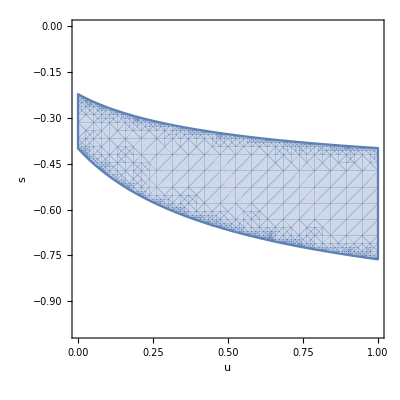

```mathematica
RegionPlot[valid[[3]],{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

```mathematica
sol2=FullSimplify[sol[[2]],Assumptions->{0<u<1,-1≤s<0}]
```

{f_0→(4+12 s+37 s^2+40 u+152 s u+142 s^2 u+108 u^2+288 s u^2+180 s^2 u^2+72 u^3+144 s u^3+72 s^2 u^3-√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2) (2 (1+u) (1+6 u)+s (9+4 u (5+3 u))))/(16 s^2 (1+u) (2+3 u)^2),f_1→1/(8 s^2 (1+u) (2+3 u)^2)(3 s^2 (1+2 u) (5+2 u (7+6 u))+2 (1+u) (1+6 u) (-2-6 u+√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))+s (-4+5 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+2 u (-26+7 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+6 u (-5+√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)))))}

```mathematica
w̄[2,s]/.Subscript[f, 2]->cum[2]/.sol2//Simplify
```

(14+3 s+18 u+6 s u+√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))/(8 (1+u) (2+3 u))

```mathematica
FullSimplify[Series[(14+3 s+18 u+6 s u+√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))/(8 (1+u) (2+3 u)),{u,0,1}],Assumptions->2-3 s>0]
```

1+(-2+2/(2-3 s)) u+O[u]^2

```mathematica
Manipulate[Plot[{(5+s+6 u+2 s u+√((-1+s)^2+4 (1+s+s^2) u+4 (1+s)^2 u^2))/(2 (1+u) (3+4 u)),(14+3 s+18 u+6 s u+√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))/(8 (1+u) (2+3 u)),1/(1+2 u)},{u,0,.1},AxesLabel->{u,ŵ},LabelStyle->Medium,PlotLegends->{"Selfing","Amitosis","Random mating"}],{{s,-.1,"s"},-.5,0,Appearance->"Labeled"}]
```

```mathematica
jac=Table[Table[D[nextf[[i]],Subscript[f, j]],{j,0,1}],{i,1,2}]//Simplify
```

{{-2 u+2/(2+2 s-2 s f_0-s f_1)+(4 s f_0)/(-2-2 s+2 s f_0+s f_1)^2,1/6+(2 s f_0)/(-2-2 s+2 s f_0+s f_1)^2},{2 (u+(s (2+s) f_1)/(-2-2 s+2 s f_0+s f_1)^2),-1/3-u+(2+s)/(2+2 s-2 s f_0-s f_1)+(s (2+s) f_1)/(-2 (1+s)+2 s f_0+s f_1)^2}}

```mathematica
jac1=jac/.sol[[1]]//Simplify
```

{{1/(1+s)-2 u,1/6},{2 u,(4+s-6 u-6 s u)/(6+6 s)}}

Characteristic polynomial

```mathematica
-jac1[[1,1]]-jac1[[2,2]]//Simplify
```

-(10+s-18 u-18 s u)/(6+6 s)

```mathematica
a1=CoefficientList[CharacteristicPolynomial[jac1,x],x]//FullSimplify
```

{(4+s-4 (1+s) (4+s) u+12 (1+s)^2 u^2)/(6 (1+s)^2),-(10+s)/(6+6 s)+3 u,1}

```mathematica
pol1[x_]:=x^2+a1[[2]]x+a1[[1]]
```

Bilinear transformation

```mathematica
b1=CoefficientList[(-1+z)^2 pol1[(z+1)/(z-1)],z]//FullSimplify
```

{(20+24 s+7 s^2-2 (1+s) (17+11 s) u+12 (1+s)^2 u^2)/(6 (1+s)^2),(2+11 s+6 s^2+4 (1+s) (4+s) u-12 (1+s)^2 u^2)/(3 (1+s)^2),(s (2+5 s))/(6 (1+s)^2)+2 u^2+(u+7 s u)/(3+3 s)}

```mathematica
stab1=Reduce[{b1[[1]]/b1[[3]]>0,b1[[2]]/b1[[3]]>0,0<u<1,-1≤s<0}]
```

Part::partd: Part specification b1⟦1⟧ is longer than depth of object.

Part::partd: Part specification b1⟦3⟧ is longer than depth of object.

Part::partd: Part specification b1⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

0<u<1&&-1≤s<0&&((b1⟦1⟧<0&&b1⟦2⟧<0&&b1⟦3⟧<0)||(b1⟦1⟧>0&&b1⟦2⟧>0&&b1⟦3⟧>0))

```mathematica
FullSimplify[√((1+6 u)/((5+14 u+12 u^2)^2))+(-1-8 u-12 u^2)/(5+14 u+12 u^2),Assumptions->0<u<1]
```

(-1-4 u (2+3 u)+√(1+6 u))/(5+2 u (7+6 u))

```mathematica
FullSimplify[√2 √((2+3 u)/((7-22 u+12 u^2)^2))-(4 (3-7 u+3 u^2))/(7-22 u+12 u^2),Assumptions->0<u<.4]
```

(-12+4 (7-3 u) u+√(4+6 u))/(7+2 u (-11+6 u))

```mathematica
RegionPlot[stab1,{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

-Graphics-

```mathematica
jac2=jac/.sol2//FullSimplify
```

{{1/(18 s (2+s))(9 s^3 (1+2 u)^2-2 (1+6 u) (-2-6 u+√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))+s (52-11 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+6 u (17+30 u-3 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)))-3 s^2 (-9+√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+2 u (-17-24 u+√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)))),1/(36 s (2+s))(9 s^3 (1+2 u)^2-3 s^2 (1+2 u) (-8-24 u+√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))-2 (1+6 u) (-2-6 u+√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))+2 s (11-4 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+3 u (20+30 u-3 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))))},{1/(9 s (2+s))(-9 s^3 u (1+2 u)+2 (1+6 u) (-2-6 u+√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))+s (-4+5 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)-3 u (8+42 u-5 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)))+3 s^2 (5+u (1-24 u+√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)))),1/(36 s (2+s))(s^3 (9-36 u^2)+4 (1+6 u) (-2-6 u+√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))+3 s^2 (26-√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+2 u (4-24 u+√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)))+s (4 (13+√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))+6 u (-14-42 u+5 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))))}}

Characteristic polynomial

```mathematica
a2=CoefficientList[CharacteristicPolynomial[jac2,x],x]//FullSimplify
```

{1/(108 (2+s)^2)(27 s^4 (1+2 u)^3+9 s^3 (1+2 u) (19-√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+2 u (35+36 u-√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)))-4 s (-197+46 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)-3 u (186-32 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+3 u (97+60 u-9 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))))+4 (134-31 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+3 u (82-16 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+3 u (38+18 u-5 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))))+3 s^2 (122-21 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+2 u (313-32 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+6 u (103+72 u-5 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))))),1/12 (-26+3 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)-3 s (3+4 u (2+u))+(2 u (-20-18 u+√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+s (-14-12 u+√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))))/(2+s)),1}

```mathematica
pol2[x_]:=x^2+a2[[2]]x+a2[[1]]
```

Bilinear transformation

```mathematica
b2=CoefficientList[(-1+z)^2 pol2[(z+1)/(z-1)],z]//FullSimplify
```

{1/(108 (2+s)^2)(27 s^4 (1+2 u)^3+9 s^3 (1+2 u) (28-√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+2 u (38+36 u-√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)))+2 s (1240-146 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+3 u (660-73 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+6 u (130+60 u-9 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))))-4 (-476+58 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)-3 u (142-19 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+3 u (56+18 u-5 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))))-6 s^2 (-172+15 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+u (-499+35 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+6 u (-121-72 u+5 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))))),1/(54 (2+s)^2)(-27 s^4 (1+2 u)^3+9 s^3 (1+2 u) (-19+√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+2 u (-35-36 u+√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)))+4 s (-89+46 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)-3 u (186-32 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+3 u (97+60 u-9 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))))+4 (-26+31 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)-3 u (82-16 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+3 u (38+18 u-5 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))))+3 s^2 (-86+21 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)-2 u (313-32 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+6 u (103+72 u-5 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))))),1/(108 (2+s)^2)(27 s^4 (1+2 u)^3-4 (-2 (1+3 u)^2 (4+9 u)+4 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+39 u √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+45 u^2 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))+6 s^2 (2+3 u) (-7-3 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+2 u (37+72 u-5 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)))+9 s^3 (1+2 u) (10-√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+2 u (32+36 u-√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)))+s (-40-76 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+6 u (84-55 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+6 u (64+60 u-9 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)))))}

```mathematica
stab2=Reduce[{b2[[1]]/b2[[3]]>0,b2[[2]]/b2[[3]]>0,0<u<1,-1≤s<0}]
```

Part::partd: Part specification b2⟦1⟧ is longer than depth of object.

Part::partd: Part specification b2⟦3⟧ is longer than depth of object.

Part::partd: Part specification b2⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

0<u<1&&-1≤s<0&&((b2⟦1⟧<0&&b2⟦2⟧<0&&b2⟦3⟧<0)||(b2⟦1⟧>0&&b2⟦2⟧>0&&b2⟦3⟧>0))

```mathematica
RegionPlot[stab2,{u,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

-Graphics-

```mathematica
k̄[2]/.Subscript[f, 2]->cum[2]/.sol2//Simplify
```

(-2+3 s-22 u+6 s u-24 u^2+√((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))/(4 s (1+u) (2+3 u))

```mathematica
𝒱[2]/.Subscript[f, 2]->cum[2]/.sol2//Simplify
```

-1/(8 s^2 (1+u)^2 (2+3 u)^2)u (12+100 s+15 s^2+160 u+376 s u+72 s^2 u+348 u^2+540 s u^2+120 s^2 u^2+216 u^3+288 s u^3+72 s^2 u^3-6 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+5 s √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+2 u √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+14 s u √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+12 u^2 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2)+12 s u^2 √((2-3 s)^2+12 (2+3 s (1+s)) u+36 (1+s)^2 u^2))

```mathematica
𝒮[2]/.Subscript[f, 2]->cum[2]/.sol2//Simplify
```

-1/(16 s^3 (1+u)^3 (2+3 u)^3)(3 s^3 (5+59 u+298 u^2+826 u^3+1320 u^4+1152 u^5+432 u^6)+4 (-2+1080 u^6+√(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2))+3 u^2 (-20+√(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2)))+108 u^5 (22+√(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2)))+3 u (-8+3 √(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2)))+13 u^3 (32+3 √(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2)))+18 u^4 (99+8 √(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2))))+12 s (-1+756 u^6+√(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2))+3 u (-3+√(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2)))+18 u^5 (103+3 √(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2)))+u^2 (161+19 √(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2)))+3 u^4 (608+33 √(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2)))+u^3 (871+66 √(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2))))+s^2 (26+6048 u^6+5 √(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2))+216 u^5 (73+√(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2)))+7 u (92+7 √(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2)))+36 u^4 (490+13 √(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2)))+u^2 (3766+200 √(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2)))+2 u^3 (5426+213 √(4 (1+3 u)^2+9 (s+2 s u)^2+12 s (-1+3 u+6 u^2)))))